# Calculation of θ(t), dθ(t) and ν(t) dependances for heteropolymers with given sequence in vacuum and in solvent (random and correlated sequences)

## Preliminary chosen data and calculations

```mathematica
(*== Notes: 
F-> "f" in the program, c-> "conc, c" in the program, N -> "n"  in the program==*)

(*== Transfer matrix for each repeated unit: M[]  ==*)
M[d_,q_,W_]:=
Normal[SparseArray[{ {1,1}->W,{d-1,d}->(q-1),{d,d}->(q-1),{i_,j_}/;j-i==1-> 1,{d,j_}-> 1},{d,d}]]; 

(*==  Eigenvalues: λ for st-the highest value Subscript[λ, 1] second high value:Subscript[λ, 2]  ==*)
ML[d_,q_,W_]:=ML[d,q,W]=Eigenvalues[M[d,q,W]];(*λ*)
ML1[d_,q_,W_]:=Abs[ML[d,q,W][[1]]];(* Subscript[λ, 1]*)
ML2[d_,q_,W_]:=Abs[ML[d,q,W][[2]]]; (* Subscript[λ, 2]*)

(*==  Base energetic parameter "W" and energetic parameter "Wcomp" where competitive interactions are taken into account  ==*)
W[u_,t_]:=ⅇ^(u/t);

Wcomp[u_,ust_,udst_,qst_,qdst_,t_]:=(ⅇ^(u/t)*(1+(ⅇ^(ust/t)-1)/qst))/(1+(ⅇ^(udst/t)-1)/qdst);


(*==  Correlation length  ==*)
Xi[d_,q_,W_]:=Abs[1/Log[ML1[d,q,W]/ML2[d,q,W]]];


(*==  Left matrix  &  right matrix  ==*)
MA[d_,q_,W_]:=Transpose[Eigenvectors[M[d,q,W]]];(*left matrix*)
MB[d_,q_,W_]:=Inverse[MA[d,q,W]];(*right matrix*)


(*==  Trasfer matrix of monomer in helix state: G' ==*)
 DW[d_,q_,W_]:=Normal[SparseArray[{ {1,1}->W},{d,d}]];  


(*== 2 differentials of characteristic equastion (L==λ -> variable) ==*)
dfdL[d_,L_, J_, Q_]:=L^(-1+d) (-ⅇ^J+L)+L^(-1+d) (L-Q)+(-1+d) L^(-2+d) (-ⅇ^J+L) (L-Q);
dfdJ[d_,L_, J_, Q_]:=ⅇ^J (1-Q)-ⅇ^J L^(-1+d) (L-Q);
dfdL[d_,q_,w_]:=dfdL[d,ML1[d,q,w],Log[w],q];dfdJ[d_,q_,w_]:=dfdJ[d,ML1[d,q,w],Log[w],q];


(*== Helicity degree: Theta1 and theta (different ways of calculation) ==*)
Theta1[d_,q_,W_]:=(MB[d,q,W]. DW[d,q,W].MA[d,q,W])[[1,1]]/ML1[d,q,W];
Theta[d_,q_,W_]:=-dfdJ[d,q,W]/dfdL[d,q,W]/ML1[d,q,W];
```

```mathematica
(*== values ==*)
(*== x-> probability of type A repeated units ,
	n0-> preliminary chosen number of repeated units,
	d-> transfer matrix dimension,
	u-> hydrogen bond's energy for A type and B type repeated units respectively-> u={Subscript[u, A],Subscript[u, B]},
	q-> number of conformations of repeated units: type A and type B respectively -> q={Subscript[q, A],Subscript[q, B]},
	t-> reduced temperature,
	data0 -> generating random sequence with probability "x"
 ==*)

(*if Ust(A)=Ust(B),Udst(A)=Udst(B) and qst(A)=qst(B),qdst(A)=qdst(B)=> non-selective interavctions *)
n=3000; d=4; u={1,0.8}; q={71,51};ust={0.2,0.1};udst={0.1,0.2};
 qst={12,10}; qdst={10,12};
 tmin=0.2; tmax=0.23; dt=(tmax-tmin)/1000;T={};
```

```mathematica
(*===   generation of the sequence  ===*)
 data=RandomReal[1,n]; x=0.5;
seq=Table[If[data[[i]]≤x, 0,1],{i,n}];  (*the sequence*)


(*x=0.5; dx=0.3; seq={}; x1=x;*)

(*
(*===   generation of the correlated sequence  ===*)
For[i=1,i≤n,i++,
ru=RandomReal[];
If[ru≤x1,x1=x+dx;data=0,x1=x-dx;data=1];
AppendTo[seq,data] (*the sequence*)
];
*)

(*
(*-- Importing a sequence --*)
seq=Flatten[Import["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_solvent/2seq.dat" ]];
*)

(*
(*-- Importing a sequence with correlation--*)
seq=Flatten[Import["//Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/32seq.dat"]];
*)

(*==  number of repeated units in imported sequence  ==*)
n=Length[seq];
n0=2;

conc=N[1/n Count[seq,0]]; (*concentration of type A nucleotides in the sequence*)
L1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]}}];
R1=Flatten[{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},1];
R2=Flatten[{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]},1];

(*--  defines matrices to fill later,    and the parameters containing "...comp" in the end indicate the same 
parameters with competitive interactions taken into account   --*)

θ={};ν={}; Htensor={};Jtensor={};T={};
θcomp={};νcomp={}; Htensorcomp={};Jtensorcomp={};Tcomp={};
νθcomp={}; νθ={};θ1={};θ2={};nu1={};nu2={};


θcomphom1={};νcomphom1={};Tcomphom1={};

θcomphom2={};νcomphom2={}; Tcomphom2={};
```

```mathematica
data
```

```mathematica
seq
```

```mathematica
(*
(*===   generation of the homopolymeric sequences  ===*)
x1=1; x2=0;
data=RandomReal[1,n];
seq1=Table[If[data[[i]]≤x1, 0,1],{i,n}];  (*the sequence*)
seq2=Table[If[data[[i]]≤x2, 0,1],{i,n}] ;
*)
```

```mathematica
(*==  Exporting sequence  ==*)
  strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"Year","Month","Day","Hour","Minute","Second"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

## Main calculations in cycle

```mathematica
For[t=tmin,t≤tmax, t+=dt,(*---   sequence of corresponding transfer-matrices Subscript[G, i]  ---*)matrseq=Table[If[seq[[i]]==0,M[d,q[[1]],W[u[[1]],t]],M[d,q[[2]],W[u[[2]],t]]],{i,n}];


(*---   Array of reduced matrices Subscript[g, i]=1/Subscript[λ, i1] Subscript[G, i]   ---*)
gi=Table[If[seq[[i]]==0,(1/ML1[d,q[[1]],W[u[[1]],t]])*matrseq[[i]],(1/ML1[d,q[[2]],W[u[[2]],t]])*matrseq[[i]]],{i,n}]; 


H=Table[ArrayFlatten[{{gi[[i]],If[seq[[i]]==0,(1/ML1[d,q[[1]],W[u[[1]],t]])*DW[d,q[[1]],W[u[[1]],t]],(1/ML1[d,q[[2]],W[u[[2]],t]])*DW[d,q[[2]],W[u[[2]],t]]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],gi[[i]]}}],{i,n}];


J=Table[ArrayFlatten[{{gi[[i]],If[seq[[i]]==0,(1/ML1[d,q[[1]],W[u[[1]],t]])*DW[d,q[[1]],W[u[[1]],t]],(1/ML1[d,q[[2]],W[u[[2]],t]])*DW[d,q[[2]],W[u[[2]],t]]].If[seq[[i+1]]==0,(1/ML1[d,q[[1]],W[u[[1]],t]])*DW[d,q[[1]],W[u[[1]],t]],(1/ML1[d,q[[2]],W[u[[2]],t]])*DW[d,q[[2]],W[u[[2]],t]]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],gi[[i+1]]}}],{i,n-1}];


(*---   sequence of corresponding transfer-matrices Subscript[G, i] 
with competitive interactions taken into account  

M[d,q[[1]],W[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]],M[d,q[[2]],W[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]],{i,n}];
---*)matrseqcomp=Table[If[seq[[i]]==0,M[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]],M[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]],{i,n}];


(*---   Array of reduced matrices Subscript[g, i]=1/Subscript[λ, i1] Subscript[G, i]  
with competitive interactions taken into account ---*)
gicomp=Table[If[seq[[i]]==0,(1/ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]])*matrseqcomp[[i]],(1/ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]])*matrseqcomp[[i]]],{i,n}]; 


Hcomp=Table[ArrayFlatten[{{gicomp[[i]],If[seq[[i]]==0,(1/ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]])*DW[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]],(1/ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]])*DW[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],gicomp[[i]]}}],{i,n}];


Jcomp=Table[ArrayFlatten[{{gicomp[[i]],If[seq[[i]]==0,(1/ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]])*DW[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]],(1/ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]])*DW[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]].If[seq[[i+1]]==0,(1/ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]])*DW[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]],(1/ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]])*DW[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],gicomp[[i+1]]}}],{i,n-1}];


(*--  2 same angular matrices to use later  --*)
prod=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];
prod1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];

(*--  2 same angular matrices to use later in calculations with competitive interactions taken into account --*)
prodcomp=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];
prod1comp=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];



H1=H[[n0-1]];J1=J[[n0-1]];
H1comp=Hcomp[[n0-1]]; J1comp=Jcomp[[n0-1]];

(*--  for each t calculating multiplication of transfer-matrices and adding gained data of mentioned "t" and matrix to "Htensor"- to calculate helicity degree (θ) later  --*)

(*== factor "2" is used to increase values as wolfram math. equates small values to zero ==*)
For[i=n0,i≤n,i++, H1=2*H1.H[[i]];


H1comp=2*H1comp.Hcomp[[i]]


];
prod=prod.H1;
AppendTo[Htensor,H1];
AppendTo[T,t];

(*--  for each t calculating multiplication of transfer-matrices and adding gained data of mentioned "t" and matrix to "Jtensor" - to calculate average length of helicity degree (ν) later  --*)

For[i=n0,i≤n-1,i++, J1=2*J1.J[[i]];


J1comp=2*J1comp.Jcomp[[i]]


];
prod1=2*prod1.J1;
AppendTo[Jtensor,J1];

(*-- calculating "Trace (Shpur)" of multiplication: "Left matrix","product of transfer-matrices" and "Right matrix" --*)
Ω=Tr[L1.prod.R1];
Ψ=Tr[L1.prod.R2]; 
Κ=Tr[L1.prod1.R2];

(*--  for each t calculating multiplication of transfer-matrices and adding gained data of mentioned "t" and matrix to "Htensor"- to calculate helicity degree (θ) later (competitive interactions taken into account)  --*)

(*
For[i=2,i≤n,i++, H1comp=H1comp.Hcomp[[i]]];
*)


prodcomp=prodcomp.H1comp;
AppendTo[Htensorcomp,H1comp];



(*--  for each t calculating multiplication of transfer-matrices and adding gained data of mentioned "t" and matrix to "Jtensor" - to calculate average length of helicity degree (ν) later
(competitive interactions taken into account)    --*)
(*
For[i=2,i≤n-1,i++, J1comp=J1comp.Jcomp[[i]]];
*)



prod1comp=2*prod1comp.J1comp;
AppendTo[Jtensorcomp,J1comp];



(*-- calculating "Trace (Shpur)" of multiplication: "Left matrix","product of transfer-matrices" and "Right matrix"
(competitive interactions taken into account)   --*)



Ωcomp=Tr[L1.prodcomp.R1];
Ψcomp=Tr[L1.prodcomp.R2]; 
Κcomp=Tr[L1.prod1comp.R2];



(*--  Collecting θ(t) and ν(t) data respectively for heteropolymer  --*)
AppendTo[θ,{t,Θ=1/n*Ψ/Ω}];

AppendTo[ν,{t,Ν=1/(1-Κ/Ψ)}];
AppendTo[νθ,{Θ=1/n*Ψ/Ω,Ν=1/(1-Κ/Ψ)}];

(*--  Collecting θcomp(t) and νcomp(t) data respectively for heteropolymer interacting competitively with solvent  --*)



AppendTo[θcomp,{t,Θcomp=1/n*Ψcomp/Ωcomp}];

AppendTo[νcomp,{t,Νcomp=1/(1-Κcomp/Ψcomp)}];
AppendTo[νθcomp,{Θcomp=1/n*Ψcomp/Ωcomp,Νcomp=1/(1-Κcomp/Ψcomp)}];

]
```

```mathematica
(*==  Calculations for homopolymer "A"  ==*)

For[t=0.233,t≤0.235, t+=0.02/1000,

(*==  getting parameters for homopolymers  ==*)
νcomphomA=ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]]/(ML1[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]]-Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]);

AppendTo[νcomphom1,{t,νcomphomA}];

AppendTo[θcomphom1,{t,Theta[d,q[[1]],Wcomp[u[[1]],ust[[1]],udst[[1]],qst[[1]],qdst[[1]],t]]}];


(*=  in case need base homopolymer - use this=*)

nu01=ML1[d,q[[1]],W[u[[1]],t]]/(ML1[d,q[[1]],W[u[[1]],t]]-W[u[[1]],t]);

AppendTo[nu1,{t,nu01}];

AppendTo[θ1,{t,Theta[d,q[[1]],W[u[[1]],t]]}];

]
```

```mathematica
(*==  calculations for homopolymer "B" ==*)
For[t=0.203,t≤0.205, t+=0.02/1000,

(*==  getting parameters for homopolymers  ==*)

νcomphomB=ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]/(ML1[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]-Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]);

AppendTo[νcomphom2,{t,νcomphomB}];

AppendTo[θcomphom2,
{t,Theta[d,q[[2]],Wcomp[u[[2]],ust[[2]],udst[[2]],qst[[2]],qdst[[2]],t]]}];



(*=  in case need base homopolymer - use this=*)

nu02=ML1[d,q[[2]],W[u[[2]],t]]/(ML1[d,q[[2]],W[u[[2]],t]]-W[u[[2]],t]);

AppendTo[nu2,{t,nu02}];

AppendTo[θ2,{t,Theta[d,q[[2]],W[u[[2]],t]]}];
]
```

## Graphs

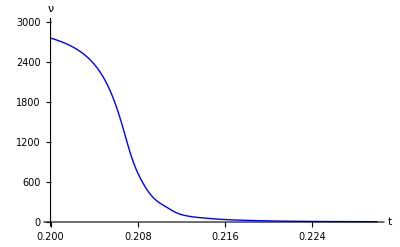

```mathematica
(*--  ν(t)dependence  --*)
nuhet=ListPlot[ν,Joined->True, PlotStyle->{Blue,Thick}, AxesLabel->{Style["t",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->{{0.2,0.23},{0,3000}}]
```

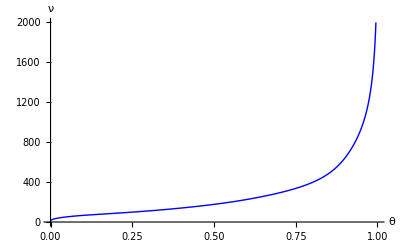

```mathematica
(*--  ν(θ)dependence base het. --*)
nuthetahet=ListPlot[νθ,Joined->True, PlotStyle->{Blue,Thick}, AxesLabel->{Style["θ",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->{{0,1},{0,2000}}]
```

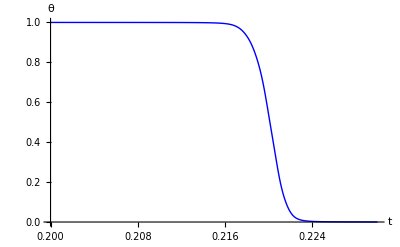

```mathematica
(*--  θ(t)dependence  --*)
Th=ListPlot[θ,Joined->True,  PlotStyle->{Blue, Thick}, AxesLabel->{Style["t",FontSize->25],Style["θ",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange->{{0.2,0.23},{0,1}}]
```

```mathematica
(*---- importing theta (vacuum) for differentiation -----*)
(*
θ={};
θ=Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/63Theta_t.dat"];

*)
```

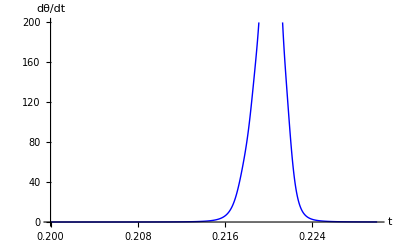

```mathematica
dθ=Table[{θ[[i,1]],-(θ[[i+1,2]]-θ[[i,2]])/(θ[[i+1,1]]-θ[[i,1]])},{i,Length[θ]-1}];

(*--  dθ(t)dependence  --*)
P=ListPlot[dθ,  Joined->True,  PlotStyle->{Blue,Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.23},{0,200}}]
```

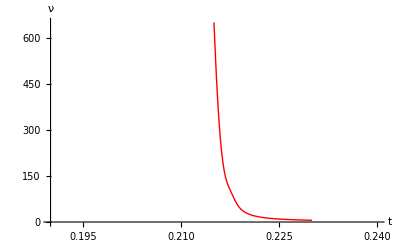

```mathematica
(*--  νcomp(t)dependence  --*)
nuhetcomp=ListPlot[νcomp,Joined->True, PlotStyle->{Red,Thick},AxesLabel->{Style["t",FontSize->2
5],Style["ν",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.19,0.24},{0,650}} ]
```

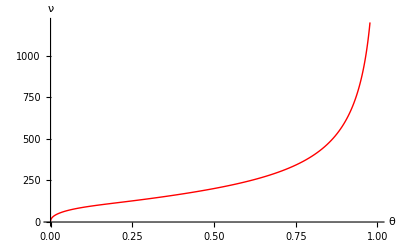

```mathematica
(*-- ν(θ)dependence for het.: competitive interactions... --*)
nuthetahetcomp=ListPlot[νθcomp,Joined->True,PlotStyle->{Red,Thick},AxesLabel->{Style["θ",FontSize->25],Style["ν",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0,1},{0,1200}}]
```

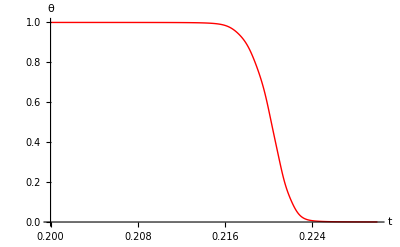

```mathematica
(*--  θcomp(t)dependence  --*)
Thcomp=ListPlot[θcomp,Joined->True,PlotStyle->{Red,Thick},AxesLabel->{Style["t",FontSize->25],Style["θ",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.23},{0,1}}]
```

```mathematica
(*---- importing theta (solvent) for differentiation -----*)
(*
θcomp={};
θcomp=Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/45Theta_t.dat"];
*)
```

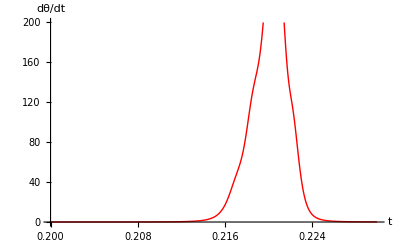

```mathematica
(*--  calculation of differential of melting temperature  --*)
dθcomp=Table[{θcomp[[i,1]],-(θcomp[[i+1,2]]-θcomp[[i,2]])/(θcomp[[i+1,1]]-θcomp[[i,1]])},{i,Length[θcomp]-1}];
(*--  dθcomp(t)dependence  --*)
Pcomp=ListPlot[dθcomp, Joined->True,PlotStyle->{Red,Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.23},{0,200}}]
```

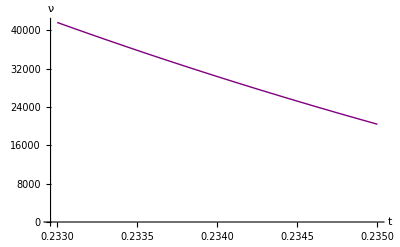

```mathematica
(*--  ν(t)dependence for homopolymer "A" --*)
nucomphom1=ListPlot[νcomphom1,Joined->True, PlotStyle->{Purple,Thick}, AxesLabel->{Style["t",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->Automatic]
```

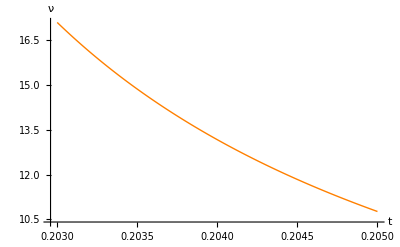

```mathematica
(*--  ν(t)dependence for homopolymer "B" --*)
nucomphom2=ListPlot[νcomphom2,Joined->True, PlotStyle->{Orange,Thick}, AxesLabel->{Style["t",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->Automatic]
```

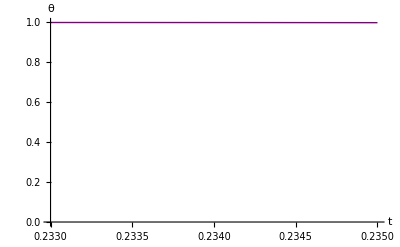

```mathematica
(*--  ν(t)dependence for homopolymer "A" --*)
thcomphom1=ListPlot[θcomphom1,Joined->True, PlotStyle->{Purple,Thick}, AxesLabel->{Style
["t",FontSize->25],Style["θ",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->{{0.233,0.235},{0,1}}]
```

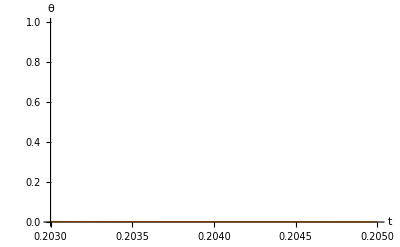

```mathematica
(*--  θ(t)dependence for homopolymer "B" --*)
thcomphom2=ListPlot[θcomphom2,Joined->True, PlotStyle->{Orange,Thick}, AxesLabel->{Style["t",FontSize->25],Style["θ",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->{{0.203,0.205},{0,1}}]
```

```mathematica
(*--  calculation of differential of melting temperature for homopolymer "A" --*)
dθcomphom1=Table[{θcomphom1[[i,1]],-(θcomphom1[[i+1,2]]-θcomphom1[[i,2]])/(θcomphom1[[i+1,1]]-θcomphom1[[i,1]])},{i,Length[θcomphom1]-1}];
(*--  dθcomp(t)dependence for homopolymer "A" --*)
Pcomphom1=ListPlot[dθcomphom1, Joined->True,PlotStyle->{Purple,Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.233,0.2342},{0,3500}}]
```

-Graphics-

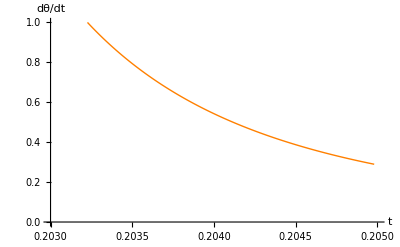

```mathematica
(*--  calculation of differential of melting temperature for homopolymer "B" --*)
dθcomphom2=Table[{θcomphom2[[i,1]],-(θcomphom2[[i+1,2]]-θcomphom2[[i,2]])/(θcomphom2[[i+1,1]]-θcomphom2[[i,1]])},{i,Length[θcomphom2]-1}];
(*--  dθcomp(t)dependence for homopolymer "B" --*)
Pcomphom2=ListPlot[dθcomphom2, Joined->True,PlotStyle->{Orange,Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.203,0.205},{0,1}}]
```

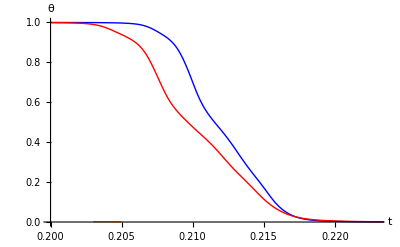

```mathematica
(*== melting curves for basic heteropolymer (blue), heteropolymer interacting with solvent (red), Homopolymer "A" (purple), homopolymer "B" orange ==*)
Show[Th, Thcomp,thcomphom1,thcomphom2, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["θ",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.223},{0,1}}, AxesOrigin->{0.2,0}]
```

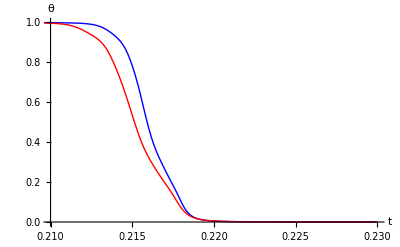

```mathematica
(*== melting curves for basic heteropolymer and interacting one ==*)
Show[Th, Thcomp, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["θ",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.21,0.23},{0,1}}, AxesOrigin->{0.21,0}]
```

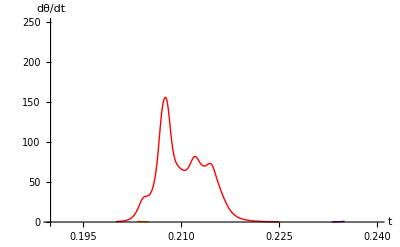

```mathematica
(*== DMC-s for heteropolymer and homopolymers ==*)
Show[ Pcomp,Pcomphom1,Pcomphom2, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.19,0.24},{0,250}},AxesOrigin->{0.19,0}]
```

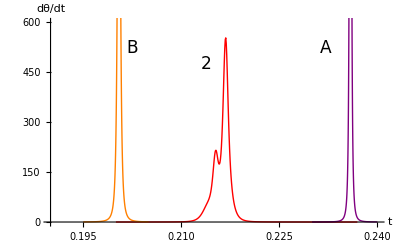

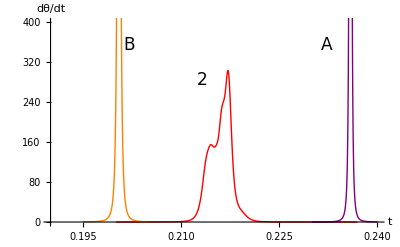

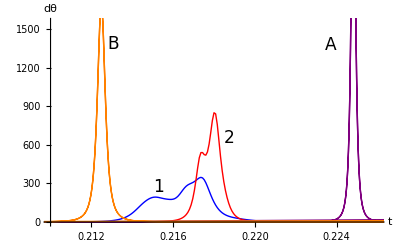

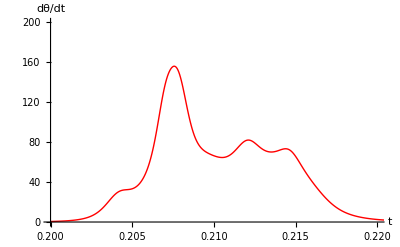

```mathematica
Show[ Pcomp, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.22},{0,200}},AxesOrigin->{0.2,0}]
```

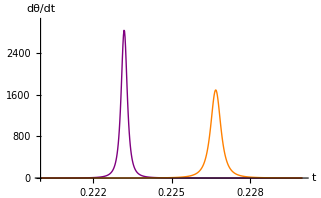

```mathematica
(*== DMC only for homopolymers interacting with solvent ==*)
Show[Pcomphom1,Pcomphom2, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.22,0.23},{0,3000}},AxesOrigin->{0.22,0}]
```

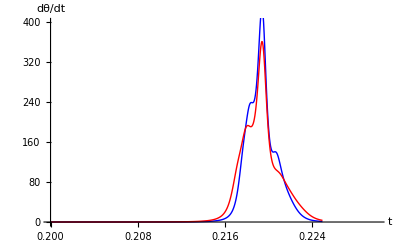

```mathematica
(*== DMC-s for basic and interacting heteropolymers ==*)
Show[P, Pcomp, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["dθ/dt",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.23},{0,400}},AxesOrigin->{0.2,0}]
```

```mathematica
(*==  dependence of average helix length on helcity degree for hom. "A":comp. int. ==*)
θνhomA=Table[{θcomphom1[[i,2]],νcomphom1[[i,2]]},{i,5000}];
nuthetahom1comp=ListPlot[θνhomA,Joined->True, PlotStyle->{Purple,Thick}, AxesLabel->{Style["θ",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->Automatic]
```

-Graphics-

```mathematica
(*==  dependence of average helix length on helcity degree for hom. "B":comp. int.  ==*)
θνhomB=Table[{θcomphom2[[i,2]],νcomphom2[[i,2]]},{i,5000}];
nuthetahom2comp=ListPlot[θνhomB,Joined->True, PlotStyle->{Orange,Thick}, AxesLabel->{Style["θ",FontSize->25],Style["ν",FontSize->25]}, AxesStyle->Directive[Black,15], PlotRange->Automatic]
```

-Graphics-

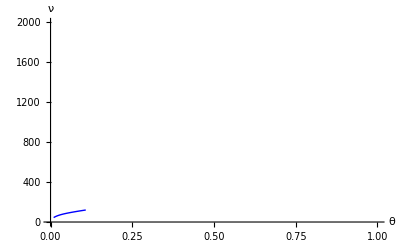
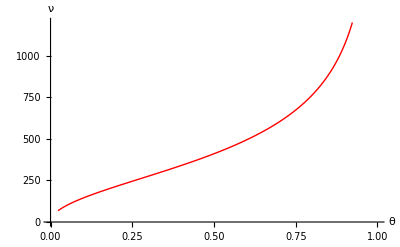
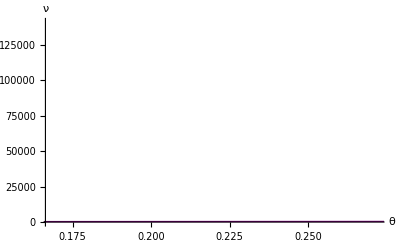
Show[-Graphics-,-Graphics-,-Graphics-,nuthetahom2comp,PlotStyle→{Thickness[Large]},AxesLabel→{θ,ν},AxesStyle→Directive[GrayLevel[0],15],PlotRange→{{0,0.99},{0,1500}},AxesOrigin→Automatic]

```mathematica
Show[nuthetahet, nuthetahetcomp,nuthetahom1comp,nuthetahom2comp, PlotStyle->{Thick},AxesLabel->{Style["θ",FontSize->25],Style["ν",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0,0.99},{0,1500}},AxesOrigin->Automatic]
```

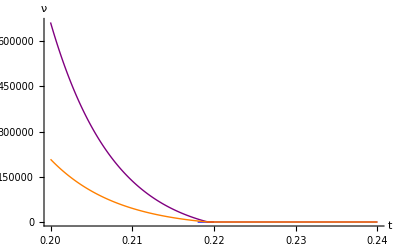

```mathematica
Show[nuhet, nuhetcomp,nucomphom1,nucomphom2, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["ν",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> Automatic,AxesOrigin->Automatic]
```

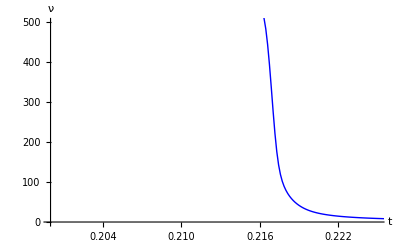

```mathematica
Show[nuhet, nuhetcomp, PlotStyle->{Thick},AxesLabel->{Style["t",FontSize->25],Style["ν",FontSize->25]},AxesStyle->Directive[Black,15], PlotRange-> {{0.2,0.225},{0,500}},AxesOrigin->{0.2,0}]
```

## Export ting data

```mathematica
(*--  Reducing matrices to the better form for exportation  --*)

Htensor=ArrayFlatten[Htensor,1];
Jtensor=ArrayFlatten[Jtensor,1];
```

```mathematica
(*--  Reducing matrices to the better form for exportation  --*)

Htensorcomp=ArrayFlatten[Htensorcomp,1];
Jtensorcomp=ArrayFlatten[Jtensorcomp,1];
```

## Random sequence data

```mathematica
(*--  exporting data {t,Htensor}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"Htr"}]<>".dat"];
WriteString[strm,ExportString[Htensor,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Jtensor}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"Jtr"}]<>".dat"];
WriteString[strm,ExportString[Jtensor,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Htensorcomp}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"Htr"}]<>".dat"];
WriteString[strm,ExportString[Htensorcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Jtensorcomp}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"Jtr"}]<>".dat"];
WriteString[strm,ExportString[Jtensorcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data T  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"T0"}]<>".dat"];
WriteString[strm,ExportString[T,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t)  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"Theta_t"}]<>".dat"];
WriteString[strm,ExportString[θ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"dtheta_t"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t)  --*)strm=OpenWrite["//Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"nu_t"}]<>".dat"];
WriteString[strm,ExportString[ν,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θcomp(t)- competitive interactins are taken into account  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"theta_t"}]<>".dat"];
WriteString[strm,ExportString[θcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθcomp(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"dtheta_t"}]<>".dat"];
WriteString[strm,ExportString[dθcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data νcomp(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"nu_t"}]<>".dat"];
WriteString[strm,ExportString[νcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*==  Exorting sequence  ==*)
(*strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/straight multiplic/me/data/" <>  DateString[Date[],{"Year","Month","Day","Hour","Minute","Second"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];*)
strm=
OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"seq"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t) for homopolymer A  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"theta_A"}]<>".dat"];
WriteString[strm,ExportString[θ1,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t) for homopolymer B  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"theta_B"}]<>".dat"];
WriteString[strm,ExportString[θ2,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θcomp(t) for homopolymer A: competitive interactions are taken into account  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"thetaA"}]<>".dat"];
WriteString[strm,ExportString[θcomphom1,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θcomp(t) for homopolymer B: competitive interactions are taken into account  --*)
strm=OpenWrite["//Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"thetaB"}]<>".dat"];
WriteString[strm,ExportString[θcomphom2,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθcomp(t)  for homopolymer "A": competitive interactions are taken into account--*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"dthetaA"}]<>".dat"];
WriteString[strm,ExportString[dθcomphom1,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθcomp(t)  for homopolymer "B": competitive interactions are taken into account--*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"dthetaB"}]<>".dat"];
WriteString[strm,ExportString[dθcomphom2,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t) for 'A'  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"nuA"}]<>".dat"];
WriteString[strm,ExportString[nu1,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t) for "B" --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/" <>  DateString[Date[],{"nuB"}]<>".dat"];
WriteString[strm,ExportString[nu2,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data νcomp(t) for 'A': competitive interactions are taken onto account  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"nuA"}]<>".dat"];
WriteString[strm,ExportString[νcomphom1,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data νcomp(t) for "B": competitive interactions are taken into account --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/" <>  DateString[Date[],{"nuB"}]<>".dat"];
WriteString[strm,ExportString[νcomphom2,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*   import

random - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_vacuum/3seq.dat


random - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_solvent/3seq.dat


correlation - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_vacuum/1seq.dat

correlation - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_solvent/1seq.dat

*)
```

## Correlated sequence data

```mathematica
(*--  exporting data {t,Htensor}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"Htr"}]<>".dat"];
WriteString[strm,ExportString[Htensor,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Jtensor}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"Jtr"}]<>".dat"];
WriteString[strm,ExportString[Jtensor,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Htensorcomp}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"Htr"}]<>".dat"];
WriteString[strm,ExportString[Htensorcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data {t,Jtensorcomp}  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"Jtr"}]<>".dat"];
WriteString[strm,ExportString[Jtensorcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data T  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"T30+"}]<>".dat"];
WriteString[strm,ExportString[T,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t)  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"Theta_t"}]<>".dat"];
WriteString[strm,ExportString[θ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"dtheta_t"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t)  --*)strm=OpenWrite["//Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/" <>  DateString[Date[],{"nu_t"}]<>".dat"];
WriteString[strm,ExportString[ν,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θcomp(t)- competitive interactins are taken into account  --*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"theta_t"}]<>".dat"];
WriteString[strm,ExportString[θcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθcomp(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"dtheta_t"}]<>".dat"];
WriteString[strm,ExportString[dθcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data νcomp(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"nu_t"}]<>".dat"];
WriteString[strm,ExportString[νcomp,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*==  Exorting sequence  ==*)
(*strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/straight multiplic/me/data/" <>  DateString[Date[],{"Year","Month","Day","Hour","Minute","Second"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];*)
strm=
OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/" <>  DateString[Date[],{"seq"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```